# Nuclear Binding Energy

```mathematica
av=15.56;15.5;
as=17.23;16.8;
ac=0.7;0.72;
asm=23.28;23;
ap =32;
(* paring *)
δ[Z_,N_]:=If[
Mod[Z+N,2]==1,0,
If[Mod[Z,2]==0 && Mod[N,2]==0, 1,
If[Mod[Z,2]==1 && Mod[N,2]==1,-1]
]
]
```

```mathematica
BE[Z_,N_,apID_]:=av (Z+N)-as(Z+N)^(2/3)-ac (Z(Z-1))/(N+Z)^(1/3)-asm(N-Z)^2/(N+Z)+apID ap δ[Z,N]/(N+Z)^(3/4)
MinZ[A_]:=Sort[Table[{z,-BE[z,A-z,1]},{z,Floor[A/3],Floor[2A/3]}],#1[[2]]<#2[[2]]&][[1;;3]]
```

```mathematica
MinZ[12]
```

{{6,-92.5101},{5,-77.2608},{7,-70.5342}}

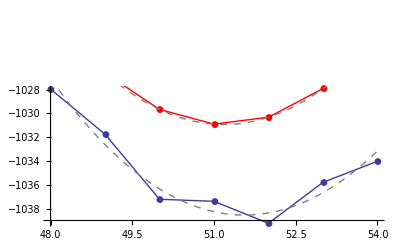

```mathematica
AA=122;
ZRange={48,54};
Show[
ListPlot[Table[{Z,-BE[Z,AA-Z,1]},{Z,ZRange[[1]],ZRange[[2]]}],PlotMarkers->{Automatic},Joined->True],
Plot[-BE[Z,AA-Z,0],{Z,ZRange[[1]],ZRange[[2]]},PlotStyle->Directive[Gray,Dashed]],
ListPlot[Table[{Z,-BE[Z,AA-1-Z,1]},{Z,ZRange[[1]],ZRange[[2]]}],PlotMarkers->{Automatic},Joined->True,PlotStyle->Red],
Plot[-BE[Z,AA-1-Z,0],{Z,ZRange[[1]],ZRange[[2]]},PlotStyle->Directive[Gray,Dashed]]
]
```

```mathematica
Remove[av,as,ac,asm,ap,δ]
```

```mathematica
(* three-point odd-even mass different *)
Collect[FullSimplify[Expand[2BE[z,n]-BE[z,n+1]-BE[z,n-1]]],{av,as,ac,asm,ap}]
Collect[FullSimplify[Expand[2BE[z,z]-BE[z,z+1]-BE[z,z-1]]],{av,as,ac,asm,ap}]
```

(8 asm z^2)/((-1+n+z) (n+z) (1+n+z))+as ((-1+n+z)^(2/3)-2 (n+z)^(2/3)+(1+n+z)^(2/3))+ac z (-1/(-1+n+z)^(1/3)+2/(n+z)^(1/3)-1/(1+n+z)^(1/3)+z (1/(-1+n+z)^(1/3)-2/(n+z)^(1/3)+1/(1+n+z)^(1/3)))+ap (-δ[z,-1+n]/(-1+n+z)^(3/4)+(2 δ[z,n])/(n+z)^(3/4)-δ[z,1+n]/(1+n+z)^(3/4))

(4 asm z)/(-1+4 z^2)+ac (-2^(2/3) (-1+z) z^(2/3)-z/(-1+2 z)^(1/3)+z^2/(-1+2 z)^(1/3)-z/(1+2 z)^(1/3)+z^2/(1+2 z)^(1/3))+as (-2 2^(2/3) z^(2/3)+(-1+2 z)^(2/3)+(1+2 z)^(2/3))+ap (-δ[z,-1+z]/(-1+2 z)^(3/4)+(2^(1/4) δ[z,z])/z^(3/4)-δ[z,1+z]/(1+2 z)^(3/4))

```mathematica
(*as *)
Manipulate[Plot[{((-1+n+z)^(2/3)-2 (n+z)^(2/3)+(1+n+z)^(2/3)),(-2 2^(2/3) z^(2/3)+(-1+2 z)^(2/3)+(1+2 z)^(2/3))},{z,1,20},PlotLabel->"surface"],{n,1,40}]
```

```mathematica
(*asm*)
Manipulate[Plot[{(8 z^2)/((-1+n+z) (n+z) (1+n+z)),(4 z)/(-1+4 z^2)},{z,1,20},PlotLabel->"Asymmetry"],{n,1,40}]
```

```mathematica
(*ac *)
Manipulate[Plot[{ (-1/(-1+n+z)^(1/3)+2/(n+z)^(1/3)-1/(1+n+z)^(1/3)+z (1/(-1+n+z)^(1/3)-2/(n+z)^(1/3)+1/(1+n+z)^(1/3))),(-2^(2/3) (-1+z) z^(2/3)-z/(-1+2 z)^(1/3)+z^2/(-1+2 z)^(1/3)-z/(1+2 z)^(1/3)+z^2/(1+2 z)^(1/3))},{z,1,20},PlotLabel->"Coulumb"],{n,1,40}]
```